# Eigenvector Continuation Demo

This notebook shows how eigenvector continuation works using simple real symmetric (Hermitian) matrices. We build a family of matrices H(c) = H0 + c H1, find the exact ground state at many values of c, then show how just three sampled eigenvectors can reproduce the whole curve.

## 1. Setup

We build two random symmetric 4 by 4 matrices, H0 and H1. H(c) is their combination for any coupling c.

```mathematica
n = 40;
SeedRandom[1];
H0 = Table[RandomReal[{-1, 1}], {n}, {n}];
H0 = (H0 + Transpose[H0])/2;
H1 = Table[RandomReal[{-1, 1}], {n}, {n}];
H1 = (H1 + Transpose[H1])/2;
H[c_] := H0 + c*H1;
```

## 2. Exact diagonalization

This function returns the lowest eigenvalue and its eigenvector for H(c), found by direct exact diagonalization.

```mathematica
ExactGround[c_] := Module[{vals, vecs, pos},
  {vals, vecs} = Eigensystem[H[c]];
  pos = Ordering[vals, 1][[1]];
  {vals[[pos]], vecs[[pos]]}
];
```

We scan c from minus 3 to 3 and record the exact ground state energy at each point.

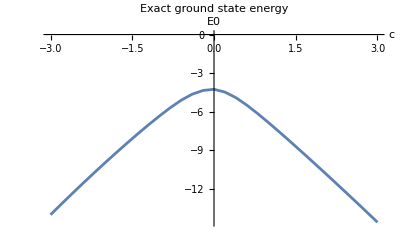

```mathematica
cRange = Table[c, {c, -3, 3, 0.2}];
exactEnergies = Table[First[ExactGround[c]], {c, cRange}];
ListLinePlot[Transpose[{cRange, exactEnergies}],
  PlotLabel -> "Exact ground state energy",
  AxesLabel -> {"c", "E0"}]
```

## 3. Eigenvector continuation

We pick just three sampling points and compute the exact ground state eigenvector at each one. These three vectors are our small basis.

```mathematica
cSample = {-2, -1, -0.5, 0, 0.5, 1, 2};
vectorsSample = Table[Last[ExactGround[c]], {c, cSample}];
basis = Transpose[vectorsSample];
```

We build the overlap matrix of the basis vectors. Then for any target c we project H(c) onto this small basis and solve the resulting small eigenvalue problem.

```mathematica
NMatrix = Transpose[basis].basis;

ECGround[c_] := Module[{HSmall, vals, vecs, pos},
  HSmall = Transpose[basis].H[c].basis;
  {vals, vecs} = Eigensystem[{HSmall, NMatrix}];
  pos = Ordering[vals, 1][[1]];
  vals[[pos]]
];
```

## 4. Compare EC vs exact

We compute the eigenvector continuation estimate at the same c values as before, using only three sampling points, and plot both curves together.

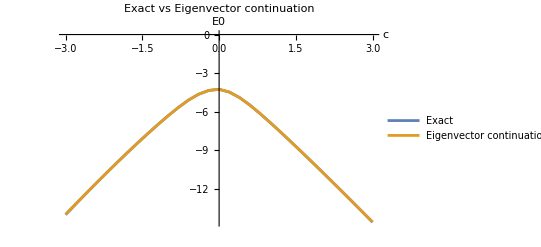

```mathematica
ecEnergies = Table[ECGround[c], {c, cRange}];

ListLinePlot[
  {Transpose[{cRange, exactEnergies}], Transpose[{cRange, ecEnergies}]},
  PlotLegends -> {"Exact", "Eigenvector continuation"},
  PlotLabel -> "Exact vs Eigenvector continuation",
  AxesLabel -> {"c", "E0"}]
```